## Coursework 1

The following two subsections contain the examples from the initial coursework assignment sheet. The solved exercises are listed below.

# Example using Plot function

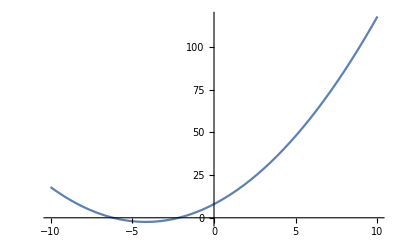

```mathematica
Plot[0.6 x^2 + 5 x + 8, {x, -10, 10}]
```

### Anti-crossing in quantum mechanics

```mathematica
symmetric2x2={{e0,v}, {v, e1}};
```

```mathematica
symmetric2x2//MatrixForm
```

(e0 | v
v | e1)

```mathematica
ham = symmetric2x2 /.{e0->x, e1->1,v->1/10};
```

```mathematica
ham // MatrixForm
```

(x | 1/10
1/10 | 1)

```mathematica
evals=Eigenvalues[ham]
```

{1/10 (5+5 x-√(26-50 x+25 x^2)),1/10 (5+5 x+√(26-50 x+25 x^2))}

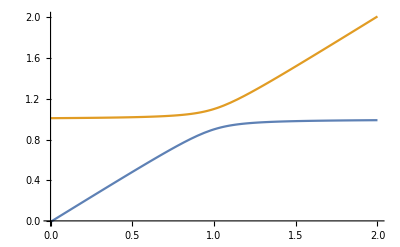

```mathematica
Plot[evals,{x,0,2}]
```

### Exercise 1: Basis state mixing

-Graphics-

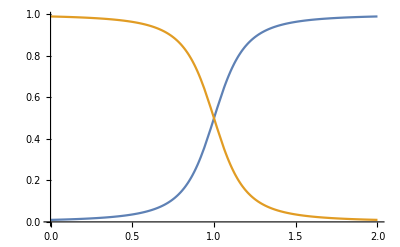

```mathematica
rules={e0->x, e1->1, v->10/100};
ham=symmetric2x2/.rules;
evals=Eigenvalues[ham];
Plot[evals,{x,0,2}]
evecs:=Eigenvectors[ham];
prob1:=Abs[Transpose[evecs][[1]]]^2;
Plot[prob1,{x,0,2}]
```

-Graphics-

-Graphics-

i) The configured Hamiltonian describes the behaviour of two energy states (e_1=1 and e_ 0=0 )  that are coupled over a 
fixed interaction potential (V=1/10). The lower initial energy state is changed linearly with a parameter x.

The upper graph shows the evolution of the energies of the new eigenstates \Psi_+ and \Psi_-  as function of x, 
here now referred as E_+  and E_-. For x=0 it is E_+ (0)=1=e_1 and E_-(0)=0 which is the initial state without an interaction.
Until about x=0.8 E_- rises linearly with x and E_+ remains roughly constant which corresponds to the behaviour of the 
initial energies without an interaction. For x>0.8 the interaction becomes relevant. The linear behavior of E_- transitions 
into constant behaviour while E_+ changes from constant to linear behaviour with f(x)=x as asymptote.

The lower graph shows the probability of measuring the initial eigenstate  in the resulting eigenstates
p_-=<\Psi_0|\Psi_- >^2 (red line) and p_+=<\Psi_0|\Psi_+>^2(blue line). For x=0 p_- is almost 1 and stays close to 1 for x<0.7
 which means that the interaction has only small influence on the final eigenstates for small x. This agrees also with 
 the energy plot where the eigenstates only differed from the initial energies for x>0.8. For x around 1, p_- drops significantly
 with a linear phase at x=1. Its slope becomes shallower while approaching p_-=0. Both probabilities are point symmetric
 in (1, 0.5) and add up to 1. This shows, that the state with increasing energy |\Psi_0> first mainly contributes to |\Psi_- >, then 
 mixes with |\Psi_1> and finally mainly contributes to the higher energy state |\Psi_+>. This can be also seen in the energy plot.

ii)

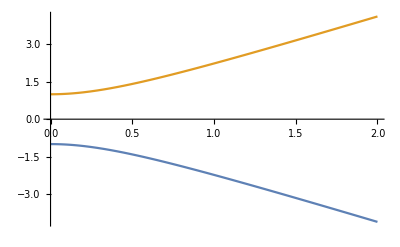

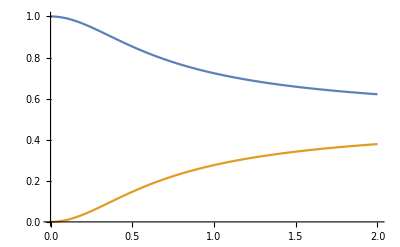

```mathematica
rules0={e0->-1, e1->1, v->2x};
ham=symmetric2x2/.rules0;
evals=Eigenvalues[ham];
Plot[evals,{x,0,2}]
evecs:=Eigenvectors[ham];
prob1:=Abs[Transpose[evecs][[1]]]^2;
Plot[prob1,{x,0,2}]
```

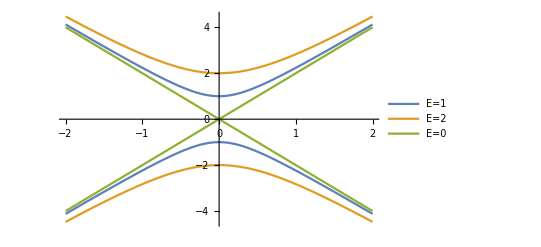

```mathematica
rules1 ={e0->-2, e1->2, v->2x};
rules2={e0->0, e1->0, v->2x};
Plot[{Eigenvalues[symmetric2x2/. rules0],Eigenvalues[symmetric2x2/. rules1],Eigenvalues[symmetric2x2/. rules2]},{x,-2,2}, PlotLegends->{"E=1", "E=2", "E=0"}]
```

### Exercise 2: Spin-spin interactions

```mathematica
echarge=1.602 10^-19(*in C*);
```

```mathematica
emass=9.11 10^-31(*in kg*);
```

```mathematica
hbar=1.05 10^-34(*in Js*);
```

```mathematica
bohrmagneton=hbar/(2 emass) 10^6 (*in µeV/T*)
```

57.629

```mathematica
r=2.793 emass/(1.673 10^-27)
```

0.00152087

```mathematica
Ehfs=5.87433 ;(*in µeV*)
B0=Ehfs / bohrmagneton (* in T*)
```

0.101934

```mathematica
H={{1/4-, 0, 0, 0},{0, -1/4-, 1/2, 0},{0, 1/2, -1/4+, 0},{0,0,0,1/4+}};
H//MatrixForm (*Hamiltonian without Ehfs factor*)
```

(1/4-x_- | 0 | 0 | 0
0 | -1/4-x_+ | 1/2 | 0
0 | 1/2 | -1/4+x_+ | 0
0 | 0 | 0 | 1/4+x_-)

v)

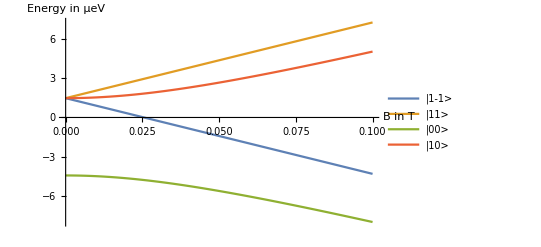

```mathematica
Heval=Ehfs H/.{->(1+r)B/B0, ->(1-r)B/B0};
energies=Eigenvalues[Heval];
Plot[energies,{B,0,0.1}, AxesLabel->{"B in T", "Energy in µeV"}, PlotLegends->{"|1-1>", "|11>","|00>","|10>"}]
```

vi)

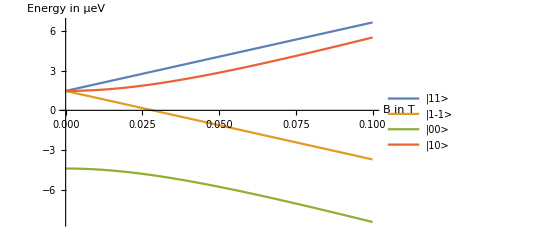

```mathematica
B1=B0;
r2=rgen;
Heval=Ehfs H/.{->(1+r2)B/B1, ->(1-r2)B/B1};
energies=Eigenvalues[Heval];
energies2=energies/.{rgen->0.1};
Plot[energies2,{B,0,0.1}, AxesLabel->{"B in T", "Energy in µeV"}, PlotLegends->{"|11>", "|1-1>","|00>","|10>"}]
```

```mathematica
Plot3D[energies, {B,0,0.1}, {rgen,0.001,2}, AxesLabel->Automatic, PlotLegends->{"|11>", "|1-1>","|00>","|10>"}]
```

-Graphics3D-

Altering B0 changes the scale of the x-axis, meaning that the slope of the functions becomes steeper with increasing it and vice versa.
Increasing r increases the energy gradient with respect to B of the states |10> and |1-1> but decreases the gradient of the |11> state. This leads to situations where the energy levels cross each other. For example at r=1 the energies of |11> and |1-1> equal each other for all B.

```mathematica
(*Heval=Ehfs H/.{->(1+x)B/B1, ->(1-x)B/B1}/.{B->0.1};
energies:=Eigenvalues[Heval]
Plot[energies,{x,1/1000,10}, AxesLabel->{"B in T", "Energy in µeV"}, PlotLegends->{"|00>", "|11>","|10>","|1-1>"}]*)
```

### Exercise 3: The Dirac Equation

```mathematica
antidiagonal=({{0, 1}, {1, 0}}); 
σx=antidiagonal;
σy=({{0, -I}, {I, 0}});
σz=({{1, 0}, {0, -1}});
αx=KroneckerProduct[antidiagonal,σx];
αy =KroneckerProduct[antidiagonal,σy];
αz=KroneckerProduct[antidiagonal,σz];
β=DiagonalMatrix[{1,1,-1,-1}];
```

```mathematica
Hdirac=αx kx+αy ky +αz kz+β m ;
Hdirac//MatrixForm
```

(m | 0 | kz | kx-ⅈ ky
0 | m | kx+ⅈ ky | -kz
kz | kx-ⅈ ky | -m | 0
kx+ⅈ ky | -kz | 0 | -m)

viii) Energy plot

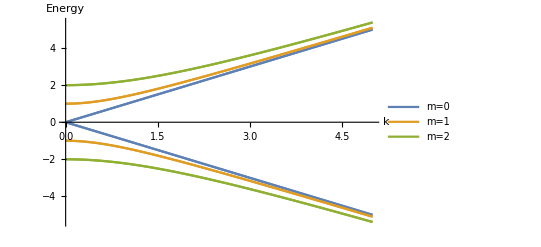

```mathematica
Heval=Hdirac/.{kz->k, kx->0, ky->0 };
evalseq=Table[Eigenvalues[Heval/.{m->i}],{i,0,2}];
Plot[evalseq,{k,0,5},AxesLabel->{"k","Energy"}, PlotLegends->{"m=0","m=1","m=2"} ]
```

ix) The energy curves can be explained over the relativistic energy-impulse relation E^2=m0^2+p^2 (natural units). Rearranging
for E gives E=sqrt(m0^2+p^2) = sqrt(m0^2+k^2). This explains why particles with mass m=0 (e.g photons) have a linear dispersion
with slope dE/dk=1=c/hbar as represented by the blue line and particles with mass m>0 approach this linear relation
asymptotically for large k. In the case of very high energies m0/p becomes negligible and the dispersion relation becomes linear with the same gradient as for m=0. 
					Approximation:

x)

```mathematica
U=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
Udagger=ConjugateTranspose[U];
Udagger.U//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
newH = Udagger.Heval.U;
newH//MatrixForm
```

(m | k | 0 | 0
k | -m | 0 | 0
0 | 0 | m | -k
0 | 0 | -k | -m)

The Hamiltonian is now in block diagonal form with 2x2 matrices of the same form as symmetric2x2 which was investigated in exercise 1. For each spin state it is e0=m, e1=-m and v=k in terms of the previous variables. This means that the lower plot shown in fig.1 from the problem sheet represents the probabilities of matter and antimatter in the new eigenstates (the factor 2 in comparison to the earlier problem is not relevant). It shows that increasing k e.g the particle momentum leads to convergence of the mixture to a 50:50 configuration for infinite particle momentum.

## Exercise 4: Graphene bandstructure

xii)

```mathematica
genham= {{0, V}, {Conjugate[V], 0}};
genham //MatrixForm
```

(0 | V
Conjugate[V] | 0)

```mathematica
grapheneHam=genham/.{V->-Eh*Exp[-I kx a]*(1+2Exp[3I kx a/2] Cos[Sqrt[3]/2 ky a])};
grapheneHam//MatrixForm
a0=0.142;
gHamEval=grapheneHam/.{Eh->2.8, a->a0};
gHamEval//MatrixForm;
```

(0 | -ⅇ^(-ⅈ a kx) Eh (1+2 ⅇ^((3 ⅈ a kx)/2) Cos[1/2 √3 a ky])
-ⅇ^(ⅈ Conjugate[a kx]) Conjugate[Eh] (1+2 ⅇ^(-3/2 ⅈ Conjugate[a kx]) Cos[1/2 √3 Conjugate[a ky]]) | 0)

```mathematica
bands=Eigenvalues[gHamEval];
Plot3D[bands, {kx, (-2Pi)/(3 a0), (+2Pi)/(3 a0)}, {ky, (-2Pi)/(Sqrt[3] a0), (2Pi)/(Sqrt[3] a0)}, AxesLabel->{"kx in nm^-1","ky in nm^-1", "Energy in eV"}]
```

-Graphics3D-

## Exercise 5

xiii)

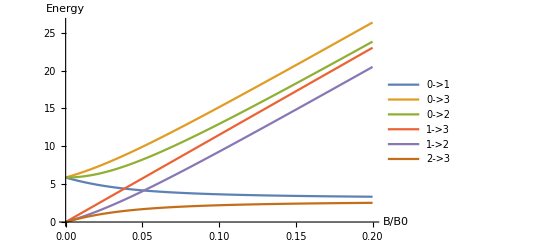

```mathematica
xplusxminus={->(1+r)B/B0, ->(1-r)B/B0};
Hnew = H Ehfs;
energies = Eigenvalues[Hnew]/.xplusxminus;
(* Plot[energies, {B, 0,1}] *)
delenergies={energies[[1]]-energies[[3]], energies[[2]]-energies[[3]], energies[[4]]-energies[[3]], energies[[2]]-energies[[1]], energies[[4]]-energies[[1]], energies[[2]]-energies[[4]]};
Plot[delenergies, {B,0,0.2}, PlotLegends->{"0->1", "0->3", "0->2", "1->3", "1->2", "2->3"}, AxesLabel->{"B/B0", "Energy"}]
```

The indices are mapped according to:  |00> -> 0, |1-1> -> 1, |10> -> 2, |11> -> 3
iv)

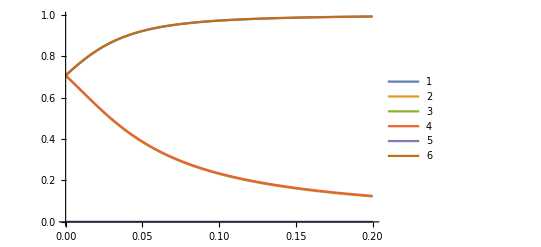

```mathematica
H//MatrixForm;
Heval10=H /.xplusxminus;
Heval10 //MatrixForm;
cdagger:=Eigenvectors[Heval10](* valid as no complex amplitudes appear *)
c:=Transpose[cdagger];
Hprime=({{0, r, 1, 0}, {r, 0, 0, 1}, {1, 0, 0, r}, {0, 1, r, 0}});
M:=cdagger.Hprime.c (*/.xplusxminus*)
offdiags:=Abs[{M[[1,2]], M[[1,3]], M[[1,4]], M[[2,3]], M[[2,4]], M[[3,4]]}]
Plot[offdiags, {B,0,0.2}, PlotLegends->Automatic]
```